Distribution of hedge (Proposition 1 in Notes)

Copula function 
The Binormal copula distribution implementation in Mathematica does not work very well, so best to implement directly.

```mathematica
Ncdf[x_]:=CDF[NormalDistribution[],x]
Ninv[p_]:=InverseCDF[NormalDistribution[],p]
```

```mathematica
CSF[u_,v_]:=CDF[CopulaDistribution[{"Binormal", 0.9}, {UniformDistribution[{0,1}], UniformDistribution[{0,1}]}],{u,v}]
FS[x_]:=Ncdf[x]
FF[x_]:=Ncdf[x]
FSInv[p_]:=Ninv[p]
```

```mathematica
CSF[u_,v_]:=CDF[CopulaDistribution[{"GumbelHougaard", 2}, {UniformDistribution[{0,1}], UniformDistribution[{0,1}]}],{u,v}]
FS[x_]:=Ncdf[x]
FF[x_]:=Ncdf[x]
FSInv[p_]:=Ninv[p]
```

### Gaussian copula

Normal margins

```mathematica
ρ=0.9;
CSF[u_,v_]:=CDF[BinormalDistribution[{0,0}, {1,1},ρ],{InverseCDF[NormalDistribution[],u],InverseCDF[NormalDistribution[],v]}]
FS[x_]:=Ncdf[x]
FF[x_]:=Ncdf[x]
FSInv[p_]:=Ninv[p]
```

```mathematica
Fh[x_]:=1-NIntegrate[Simplify[D[CSF[w,FF[(FSInv[w2]-x)/h]],w]/.w2->w], {w,0,1}]
```

```mathematica
Fh[0.5]
```

0.868224

```mathematica
CDF[NormalDistribution[0,Sqrt[1+h-2 ρ h]],0.5]
```

0.868224

```mathematica
t=Table[{x,Fh[x]}, {x,-3,3, 0.1}];
```

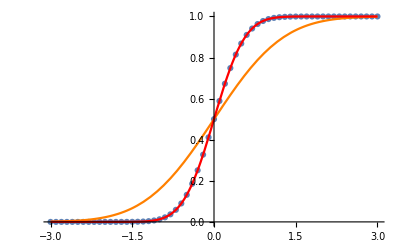

```mathematica
Show[
ListPlot[t, PlotStyle->Large],
Plot[Ncdf[x], {x,-3,3},PlotStyle->Orange],
Plot[CDF[NormalDistribution[0,Sqrt[1+h - 2 ρ h]],x], {x,-3,3}, PlotStyle->Red] 
]
```

Non-normal margins

```mathematica
ρ=0.9;
CSF[u_,v_]:=CDF[BinormalDistribution[{0,0}, {1,1},ρ],{InverseCDF[NormalDistribution[],u],InverseCDF[NormalDistribution[],v]}]
FS[x_]:=CDF[ExponentialDistribution[1],x]
FF[x_]:=CDF[StudentTDistribution[10],x]
FSInv[p_]:=InverseCDF[ExponentialDistribution[1],p]
```

```mathematica
Fh[x_]:=1-NIntegrate[Simplify[D[CSF[w,FF[(FSInv[w2]-x)/h]],w]/.w2->w], {w,0,1}]
```

```mathematica
Fh2[x_]:=1-∫_0^1 Ncdf[(Ninv[FF[(FSInv[w]-x)/h]]-ρ Ninv[w])/(√(1-ρ^2))]ⅆw
```

```mathematica
Fh2[x_]:=1-NIntegrate[Ncdf[(Ninv[FF[(FSInv[w]-x)/h]]-ρ Ninv[w])/(√(1-ρ^2))], {w,0,1}]
```

```mathematica
Timing[Fh[0.5]]
```

{0.793235,0.207144}

```mathematica
Timing[Fh2[0.5]]
```

{0.026741,0.207144}

```mathematica
X1=RandomVariate[ExponentialDistribution[1],10000];
X2=RandomVariate[StudentTDistribution[10],10000];
Y1=Ninv[CDF[ExponentialDistribution[1],X1]];
Y2=Ninv[CDF[StudentTDistribution[10],X2]];
RS=X1;
RF = ρ Y1 + Sqrt[1-ρ^2] Y2;
Z=RS-h RF;
```

```mathematica
Timing[t=Table[{x,Fh[x]}, {x,-3,3, 0.1}];]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {0.99228}. NIntegrate obtained 0.0994934 and 9.97995×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {0.99228}. NIntegrate obtained 0.0814937 and 1.4633×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {0.99228}. NIntegrate obtained 0.0669183 and 2.02413×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{34.2743,Null}

```mathematica
Timing[t2=Table[{x,Fh2[x]}, {x,-3,3, 0.1}];]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {0.99228}. NIntegrate obtained 0.0994934 and 9.97995×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {0.99228}. NIntegrate obtained 0.0814937 and 1.4633×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {0.99228}. NIntegrate obtained 0.0669183 and 2.02413×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{1.96507,Null}

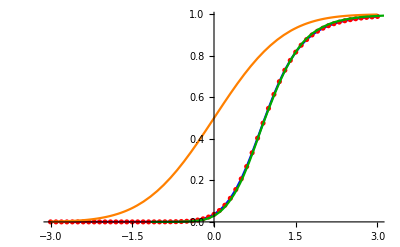

```mathematica
Show[
ListPlot[{t,t2},PlotStyle->{Blue,Red}, Joined->{True,False}],
Plot[CDF[NormalDistribution[],x], {x,-3,3},PlotStyle->Orange],
SmoothHistogram[Z,Automatic,"CDF", PlotStyle->Darker[Green]]
]
```

### Student t copula

The Student t distribution arises as a normal variance mixture where the mixing variable is inverse gamma with parameter 1/2 ν, 1/2 ν.

Student t margins

```mathematica
ρ=0.9;
ν=10;
h=1;
CSF[u_,v_]:=CDF[MultivariateTDistribution[{0,0}, {{1,ρ},{ρ,1}},ν],{InverseCDF[StudentTDistribution[ν],u],InverseCDF[StudentTDistribution[ν],v]}]
FS[x_]:=CDF[StudentTDistribution[ν],x]
FF[x_]:=CDF[StudentTDistribution[ν],x]
FSInv[p_]:=InverseCDF[StudentTDistribution[ν],p]
```

```mathematica
PDFBivariateT[x_,y_]:=NIntegrate[w^(-1)/((2 Pi) Det[{{1,ρ}, {ρ,1}}]^(1/2)) Exp[-({x,y}.MatrixPower[{{1,ρ}, {ρ,1}},-1].{x,y})/(2 w)] PDF[InverseGammaDistribution[1/2 ν, 1/2 ν],w], {w,0,∞}]
```

```mathematica
CDFBivariateT[x_,y_]:=NIntegrate[NIntegrate[PDFBivariateT[z1,z2],{z2,-∞,y}], {z1,-∞,x}]
```

```mathematica
{Timing[PDFBivariateT[.5,.5]], Timing[PDF[MultivariateTDistribution[{{1,ρ}, {ρ,1}}, ν],{.5,.5}]]}
```

(0.01022 | 0.312433
0.000353 | 0.312433)

```mathematica
Fh[x_]:=1-NIntegrate[Simplify[D[CSF[w,FF[(FSInv[w2]-x)/h]],w]/.w2->w], {w,0,1}]
```

```mathematica
D[CSF[w,FF[(FSInv[w2]-x)/h]],w]/.{w2->w, w->.5}
```

$Aborted[]

```mathematica
D[CSF[u,v],u]
```

23+(21875 ({ | 1) (1/1+1))/(32 (1^2+10)^(9/2)) if 0≤u≤1∧0≤v≤1
 |  |  |  |

```mathematica
Fh[0.5]
```

$Aborted

```mathematica
CSF[.5,.5]
```

0.428217

```mathematica
CDF[NormalDistribution[0,Sqrt[1+h-2 ρ h]],0.5]
```

0.868224

```mathematica
t=Table[{x,Fh[x]}, {x,-3,3, 0.1}];
```

```mathematica
Show[
ListPlot[t, PlotStyle->Large],
Plot[Ncdf[x], {x,-3,3},PlotStyle->Orange],
Plot[CDF[NormalDistribution[0,Sqrt[1+h - 2 ρ h]],x], {x,-3,3}, PlotStyle->Red] 
]
```

-Graphics-

Non-normal margins

```mathematica
ρ=0.9;
CSF[u_,v_]:=CDF[BinormalDistribution[{0,0}, {1,1},ρ],{InverseCDF[NormalDistribution[],u],InverseCDF[NormalDistribution[],v]}]
FS[x_]:=CDF[ExponentialDistribution[1],x]
FF[x_]:=CDF[StudentTDistribution[10],x]
FSInv[p_]:=InverseCDF[ExponentialDistribution[1],p]
```

```mathematica
Fh[x_]:=1-NIntegrate[Simplify[D[CSF[w,FF[(FSInv[w2]-x)/h]],w]/.w2->w], {w,0,1}]
```

```mathematica
Fh2[x_]:=1-∫_0^1 Ncdf[(Ninv[FF[(FSInv[w]-x)/h]]-ρ Ninv[w])/(√(1-ρ^2))]ⅆw
```

```mathematica
Fh2[x_]:=1-NIntegrate[Ncdf[(Ninv[FF[(FSInv[w]-x)/h]]-ρ Ninv[w])/(√(1-ρ^2))], {w,0,1}]
```

```mathematica
Timing[Fh[0.5]]
```

{0.793235,0.207144}

```mathematica
Timing[Fh2[0.5]]
```

{0.026741,0.207144}

```mathematica
X1=RandomVariate[ExponentialDistribution[1],10000];
X2=RandomVariate[StudentTDistribution[10],10000];
Y1=Ninv[CDF[ExponentialDistribution[1],X1]];
Y2=Ninv[CDF[StudentTDistribution[10],X2]];
RS=X1;
RF = ρ Y1 + Sqrt[1-ρ^2] Y2;
Z=RS-h RF;
```

```mathematica
Timing[t=Table[{x,Fh[x]}, {x,-3,3, 0.1}];]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {0.99228}. NIntegrate obtained 0.0994934 and 9.97995×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {0.99228}. NIntegrate obtained 0.0814937 and 1.4633×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {0.99228}. NIntegrate obtained 0.0669183 and 2.02413×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{34.2743,Null}

```mathematica
Timing[t2=Table[{x,Fh2[x]}, {x,-3,3, 0.1}];]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {0.99228}. NIntegrate obtained 0.0994934 and 9.97995×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {0.99228}. NIntegrate obtained 0.0814937 and 1.4633×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {0.99228}. NIntegrate obtained 0.0669183 and 2.02413×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{1.96507,Null}

```mathematica
Show[
ListPlot[{t,t2},PlotStyle->{Blue,Red}, Joined->{True,False}],
Plot[CDF[NormalDistribution[],x], {x,-3,3},PlotStyle->Orange],
SmoothHistogram[Z,Automatic,"CDF", PlotStyle->Darker[Green]]
]
```

-Graphics-